```mathematica
LJ[x_,s_,e_]:=4*e*((s/x)^12-(s/x)^6)
```

```mathematica
Plot[LJ[x,1,1],{x,0,3},PlotRange->{-2,4},FrameLabel->{Style["r/σ",44],Style["U(r)/ε",44]},Frame->True,LabelStyle->Directive[Large],PlotStyle->Thickness[0.005]]
```

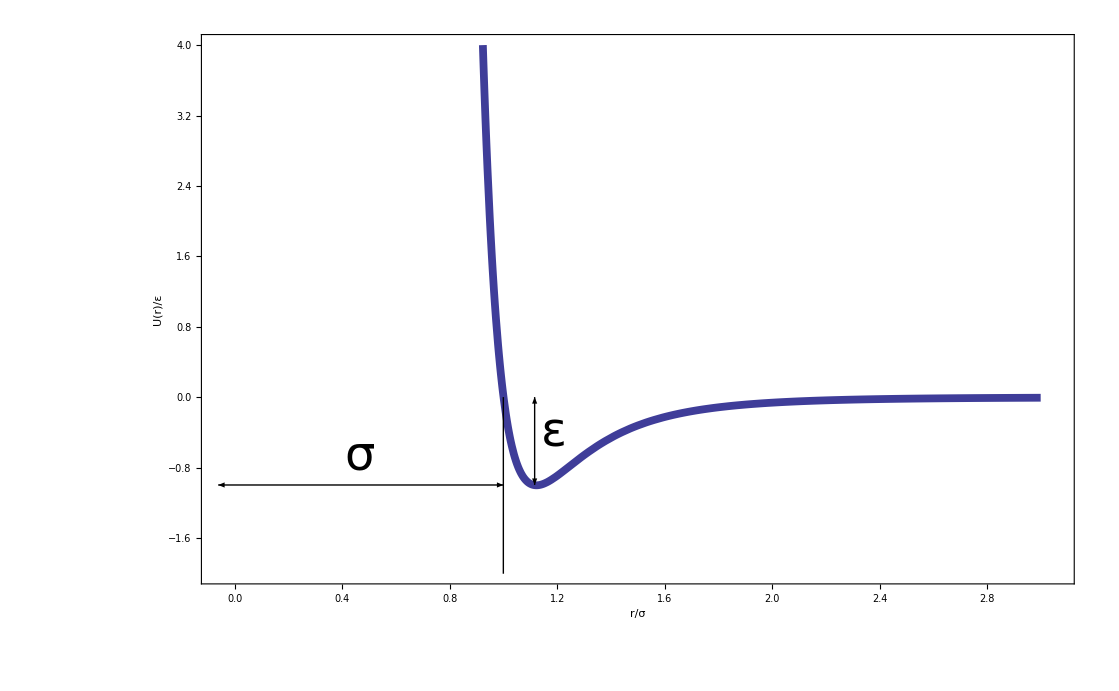

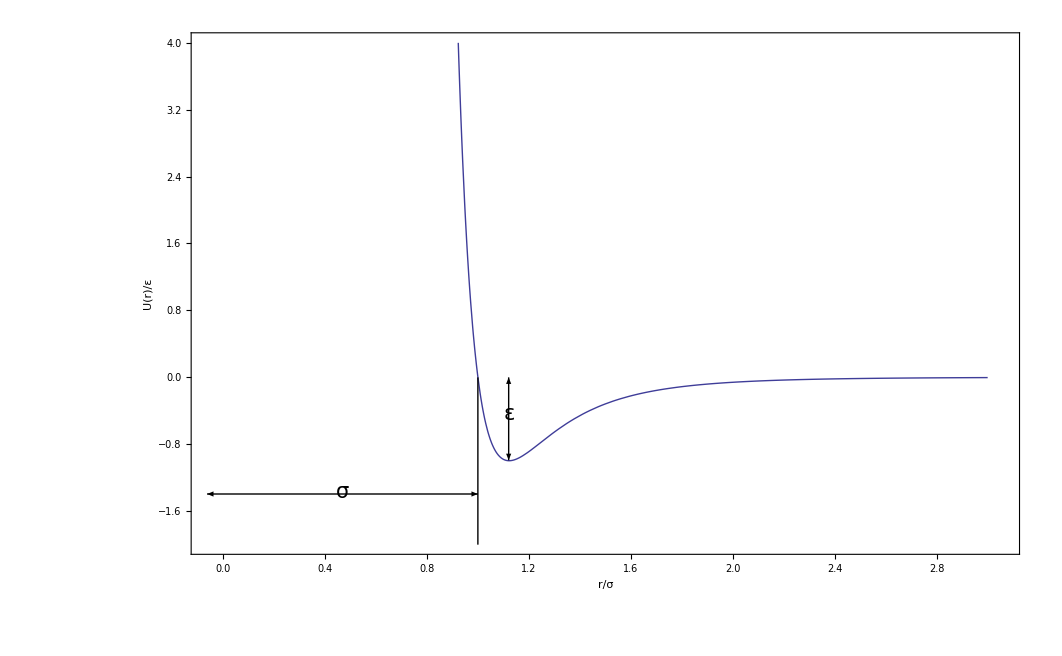

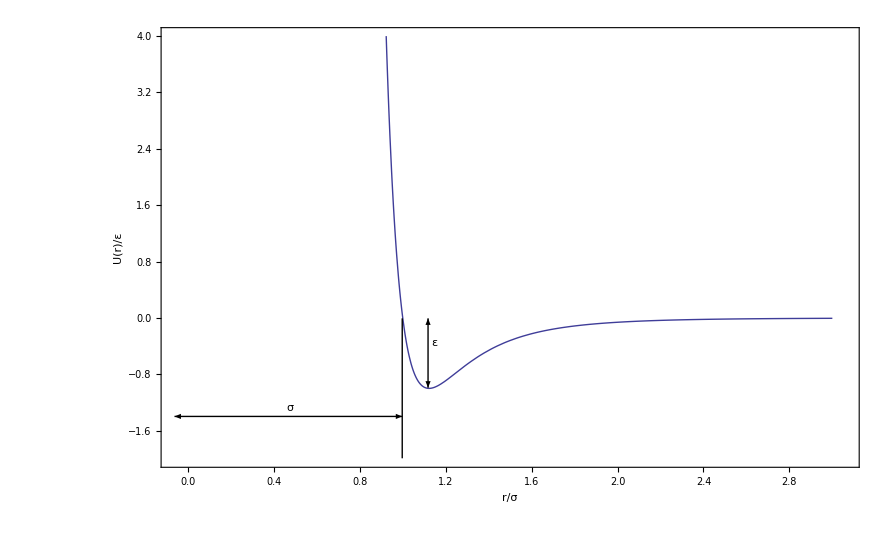

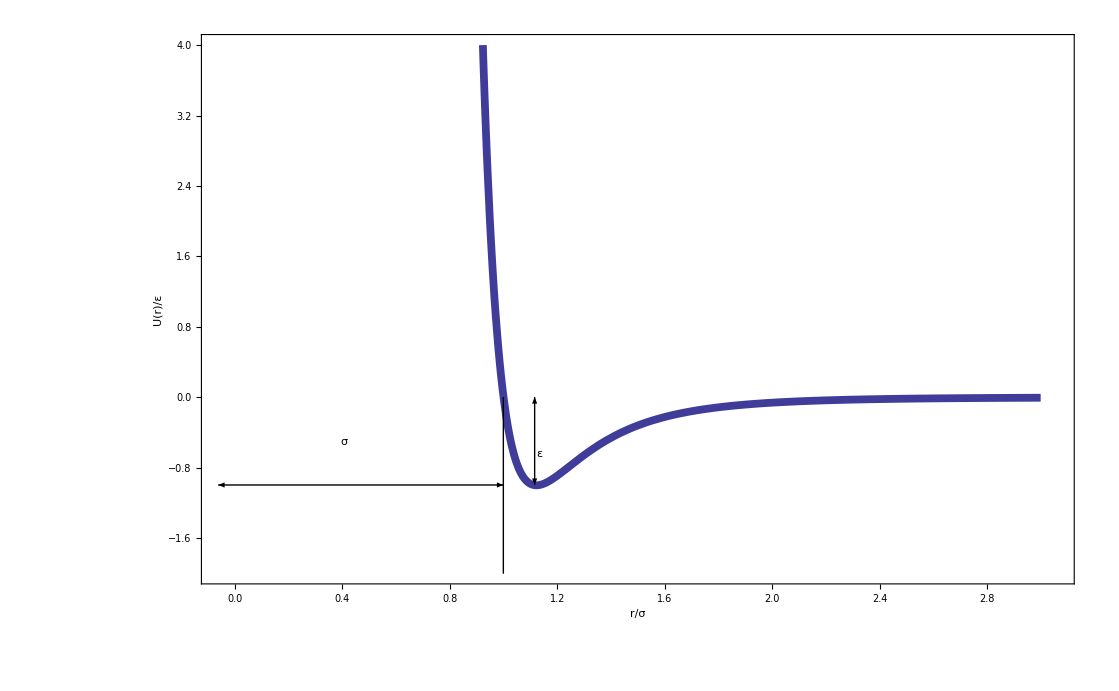
```mathematica
Export["/home/motz/codes/OpticalTweezer/doc/LJ-2.pdf",-Graphics-]
```

/home/motz/codes/OpticalTweezer/doc/LJ-2.pdf